```mathematica
colorsNew ={"#006400","#00008b", "#b03060","#ff4500","#ffd700","#7fff00","#00ffff","#ff00ff","#6495ed"}(*"#ffdab9"}*)
```

{#006400,#00008b,#b03060,#ff4500,#ffd700,#7fff00,#00ffff,#ff00ff,#6495ed}

```mathematica
hexToRGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&
```

RGBColor@@IntegerDigits[FromDigits[StringDrop[#1,1],16],256,3]/255.&

```mathematica
mColordsNew = hexToRGB[#]&/@ colorsNew
```

{RGBColor[0., 0.39215686274509803, 0.],RGBColor[0., 0., 0.5450980392156862],RGBColor[0.6901960784313725, 0.18823529411764706, 0.3764705882352941],RGBColor[1., 0.27058823529411763, 0.],RGBColor[1., 0.8431372549019608, 0.],RGBColor[0.4980392156862745, 1., 0.],RGBColor[0., 1., 1.],RGBColor[1., 0., 1.],RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824]}

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Dropbox\UNI\Projekte\A02_MCWD_Dataset_Analysis\2021\Analysis\Figure2

```mathematica
data05010 =Import["2005-2010Areas.tsv"];
data0501016 =Import["2005-2010-2016Areas.tsv"];
```

```mathematica
scens05010 = DeleteDuplicates[Rest[data05010[[All,3]]]]
```

{CHIRPS,CRU NCEP,ERA 5,GLDAS,GPCC,TRMM 6,TRMM 7,GSWP 3,WATCH WFDEI}

```mathematica
scens0501016 = DeleteDuplicates[Rest[data0501016[[All,3]]]]
```

{CHIRPS,CRU NCEP,ERA 5,GLDAS,TRMM 7,GPCC}

```mathematica
Length@mColordsNew
```

9

```mathematica
scens05010//Length
```

9

```mathematica
cList=Transpose[{Join[scens05010,{"Lewis et al. 2011"}],Join[mColordsNew,{{Black,Dashed}}]}]
```

{{CHIRPS,RGBColor[0., 0.39215686274509803, 0.]},{CRU NCEP,RGBColor[0., 0., 0.5450980392156862]},{ERA 5,RGBColor[0.6901960784313725, 0.18823529411764706, 0.3764705882352941]},{GLDAS,RGBColor[1., 0.27058823529411763, 0.]},{GPCC,RGBColor[1., 0.8431372549019608, 0.]},{TRMM 6,RGBColor[0.4980392156862745, 1., 0.]},{TRMM 7,RGBColor[0., 1., 1.]},{GSWP 3,RGBColor[1., 0., 1.]},{WATCH WFDEI,RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824]},{Lewis et al. 2011,{GrayLevel[0],Dashing[{Small,Small}]}}}

```mathematica
colsNew2016 =Table[Select[cList, #[[1]] ==scens0501016[[i]]&],{i,1,Length@scens0501016}][[All,1,2]]
```

{RGBColor[0., 0.39215686274509803, 0.],RGBColor[0., 0., 0.5450980392156862],RGBColor[0.6901960784313725, 0.18823529411764706, 0.3764705882352941],RGBColor[1., 0.27058823529411763, 0.],RGBColor[0., 1., 1.],RGBColor[1., 0.8431372549019608, 0.]}

```mathematica
p2005 = Select[data05010,#[[2]]==2005&&#[[1]]==1&][[All,7]]
```

{0.991507,1.60381,0.71778,1.16657,1.26773,1.20606,1.12809,1.28415,1.32828}

```mathematica
p2010 = Select[data05010,#[[2]]==2010&&#[[1]]==1&][[All,7]]
```

{1.4321,1.28961,1.83711,1.50991,1.28948,1.96837,1.51076,1.42521,1.2655}

```mathematica
p2016 = Select[data0501016,#[[2]]==2016&&#[[1]]==1&][[All,7]]
```

{1.14575,1.09977,1.13812,1.85526,1.42584,1.50372}

```mathematica
lewis[2005] = {1.6, 0.8, 2.6}
```

{1.6,0.8,2.6}

```mathematica
lewis[2010] = {2.2, 1.2, 3.4}
```

{2.2,1.2,3.4}

```mathematica
s5 =Table[{{2005+ (RandomReal[]*0.1-0.05), p2005[[i]]}},{i,1,Length@p2005}]
```

{{{2005.02,0.991507}},{{2004.99,1.60381}},{{2004.97,0.71778}},{{2004.99,1.16657}},{{2004.98,1.26773}},{{2005.05,1.20606}},{{2004.99,1.12809}},{{2005.05,1.28415}},{{2004.95,1.32828}}}

```mathematica
s10 =Table[{{2010+ RandomReal[]*0.7, p2010[[i]]}},{i,1,Length@p2005}]
```

{{{2010.19,1.4321}},{{2010.17,1.28961}},{{2010.45,1.83711}},{{2010.48,1.50991}},{{2010.46,1.28948}},{{2010.45,1.96837}},{{2010.61,1.51076}},{{2010.29,1.42521}},{{2010.35,1.2655}}}

```mathematica
s16 =Table[{{2016+ RandomReal[]*0.7, p2016[[i]]}},{i,1,Length@p2016}]
```

{{{2016.54,1.14575}},{{2016.06,1.09977}},{{2016.39,1.13812}},{{2016.25,1.85526}},{{2016.53,1.42584}},{{2016.19,1.50372}}}

```mathematica
Needs["ErrorBarPlots`"]
```

ErrorListPlot::shdw: Symbol "ErrorListPlot" appears in multiple contexts {"ErrorBarPlots`", "Global`"}; definitions in context "ErrorBarPlots`" may shadow or be shadowed by other definitions.

ErrorBar::shdw: Symbol "ErrorBar" appears in multiple contexts {"ErrorBarPlots`", "Global`"}; definitions in context "ErrorBarPlots`" may shadow or be shadowed by other definitions.

ErrorBar::shdw: Symbol "<ErrorBar>" appears in multiple contexts {"<ErrorBarPlots`>", "<Global`>"}; definitions in context "<ErrorBarPlots`>" may shadow or be shadowed by other definitions. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/shdw",
ButtonNote->"ErrorBarPlots`ErrorBar::shdw"]

ErrorListPlot::shdw: Symbol "ErrorListPlot" appears in multiple contexts {"ErrorBarPlots`", "Global`"}; definitions in context "ErrorBarPlots`" may shadow or be shadowed by other definitions.

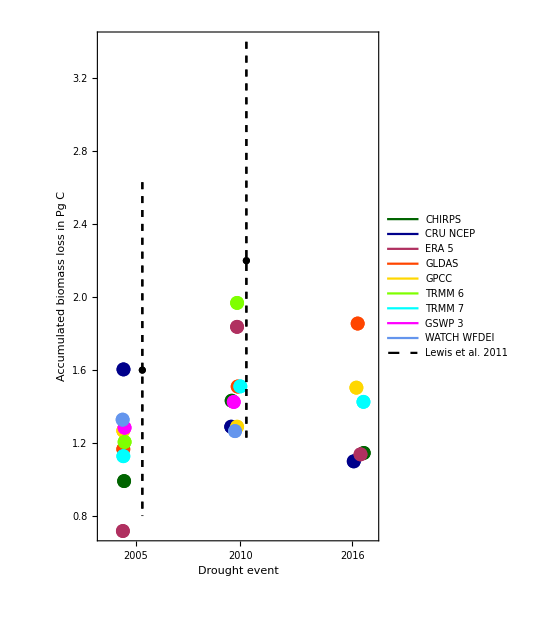

```mathematica
siFig =Legended[Show[
ErrorListPlot[{{{2005.9,1.6},ErrorBar[{-0.8,1.0299999999999998}]}}, PlotStyle->{Black, Dashed}],
ErrorListPlot[{{{2010.9,2.2},ErrorBar[{-1.0,1.2}]}}, PlotStyle->{Black, Dashed}],
ListPlot[Flatten[{s5,s10},1], PlotStyle->Table[{PointSize[0.025],mColordsNew[[i]]},{i,1,Length@s5}]],
 ListPlot[s16, PlotStyle->Table[{PointSize[0.025],colsNew2016[[i]]},{i,1,Length@s16}]], PlotRange-> {{2004,2017},All}, AxesOrigin->{2004, 0.7}, Frame->True, AspectRatio->1.6, FrameLabel-> {"Drought event", "Accumulated biomass loss in Pg C"}, LabelStyle-> Directive[12, "Arial",Black], FrameTicks->{{All,None},{{{2005.6, "2005"},{2010.6, "2010"},{2016,2016}},None}}], LineLegend[cList[[All,2]],cList[[All,1]], LegendLayout->{"Column",1}]]
```

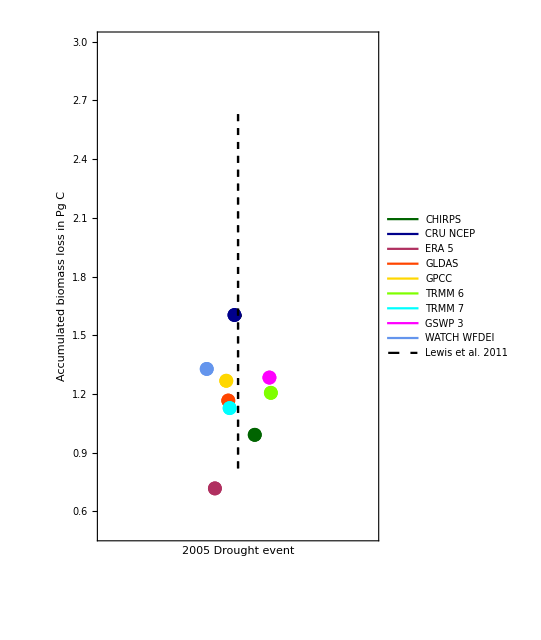

```mathematica
siFig =Legended[Show[
ErrorListPlot[{{{2005,1.6},ErrorBar[{-0.8,1.0299999999999998}]}}, PlotStyle->{Black, Dashed}],
ErrorListPlot[{{{2010.9,2.2},ErrorBar[{-1.0,1.2}]}}, PlotStyle->{Black, Dashed}],
ListPlot[Flatten[{s5,s10},1], PlotStyle->Table[{PointSize[0.025],mColordsNew[[i]]},{i,1,Length@s5}]],
 ListPlot[s16, PlotStyle->Table[{PointSize[0.025],colsNew2016[[i]]},{i,1,Length@s16}]], PlotRange-> {{2004.8,2005.2},{0.5, 3.0}}, AxesOrigin->{2004, 0.7}, Frame->True, AspectRatio->1.6, FrameLabel-> {"2005 Drought event", "Accumulated biomass loss in Pg C"}, LabelStyle-> Directive[12, "Arial",Black], FrameTicks->{{All,None},{{{2005.6, "2005"},{2010.6, "2010"},{2016,2016}},None}}], LineLegend[cList[[All,2]],cList[[All,1]], LegendLayout->{"Column",1}]]
```

```mathematica
Export["BiomassLoss fig.png", siFig, ImageResolution-> 600]
```

BiomassLoss fig.png

```mathematica
p2005//Mean
```

1.18822

```mathematica
Round[p2005, 0.05]
```

{1.,1.6,0.7,1.15,1.25,1.2,1.15,1.3,1.35}

```mathematica
Round[p2005- Mean@p2005, 0.05]
```

{-0.2,0.4,-0.45,0.,0.1,0.,-0.05,0.1,0.15}

```mathematica
cList[[All,1]]
```

{CHIRPS,CRU NCEP,ERA 5,GLDAS,GPCC,TRMM 6,TRMM 7,GSWP 3,WATCH WFDEI,Lewis et al. 2011}

```mathematica
p2010
```

{1.4321,1.28961,1.83711,1.50991,1.28948,1.96837,1.51076,1.42521,1.2655}

```mathematica
p2010- Mean@p2010
```

{-0.0710179,-0.213509,0.33399,0.00679491,-0.213635,0.465257,0.00764538,-0.0779074,-0.237618}

```mathematica
p2010
```

{1.4321,1.28961,1.83711,1.50991,1.28948,1.96837,1.51076,1.42521,1.2655}

```mathematica
Round[p2016, 0.1]
```

{1.1,1.1,1.1,1.9,1.4,1.5}

```mathematica
mColordsNew
```

{RGBColor[0., 0.39215686274509803, 0.],RGBColor[0., 0., 0.5450980392156862],RGBColor[0.6901960784313725, 0.18823529411764706, 0.3764705882352941],RGBColor[1., 0.27058823529411763, 0.],RGBColor[1., 0.8431372549019608, 0.],RGBColor[0.4980392156862745, 1., 0.],RGBColor[0., 1., 1.],RGBColor[1., 0., 1.],RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824],RGBColor[1., 0.8549019607843137, 0.7254901960784313]}

```mathematica
Export["SiFig2.png", siFig, ImageResolution-> 600]
```

SiFig2.png

```mathematica
colors={"#2e8b57","#ff0000","#ffd700","#c71585","#00ff00","#0000ff","#1e90ff"}
```

{#2e8b57,#ff0000,#ffd700,#c71585,#00ff00,#0000ff,#1e90ff}

```mathematica
TableForm[Round[Transpose@{p2005},0.01], TableHeadings->{scens05010}]
```

CHIRPS | 0.99
CRU NCEP | 1.6
ERA 5 | 0.72
GLDAS | 1.17
GPCC | 1.27
TRMM 6 | 1.21
TRMM 7 | 1.13
GSWP 3 | 1.28
WATCH WFDEI | 1.33

```mathematica
Mean[
```

```mathematica
TableForm[Round[Transpose@{p2005-1.2},0.01], TableHeadings->{scens05010}]
```

CHIRPS | -0.21
CRU NCEP | 0.4
ERA 5 | -0.48
GLDAS | -0.03
GPCC | 0.07
TRMM 6 | 0.01
TRMM 7 | -0.07
GSWP 3 | 0.08
WATCH WFDEI | 0.13

```mathematica
an[data_]:=  ToString@Round[#@data,0.01]&/@{Min, Max, Mean, Median, StandardDeviation,zSD}
```

```mathematica
an[p2005]
```

{1.25,1.91,1.59,1.59,0.19,0.29}

```mathematica
TableForm[Transpose@{an[p2005]}, TableHeadings->{ {Min, Max, Mean,Median, StandardDeviation,zSD}}]
```

Min | 0.72
Max | 1.6
Mean | 1.19
Median | 1.21
StandardDeviation | 0.24
zSD | 0.27